Max Mensah
11/21/2019
Lab 10

```mathematica
Clear[g]
g[x_]:=1/(x-1)^(1/2)
Plot[g[x],{x,0,5},PlotStyle->Red]
```

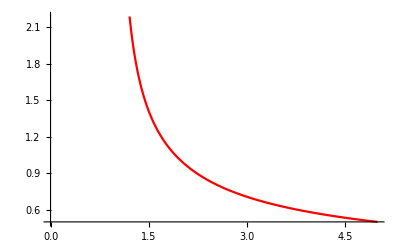
```mathematica
-Graphics-Convergent
```

```mathematica
Integrate[f[x],{x,c,1},Assumptions->1<c<5]
int[c_]:=Integrate[g[x],{x,c,5}, Assumptions->1<c<5]
Limit[int[c],c->1,Direction->-1]
```

Integrate[f[x],{x,c,1},Assumptions→1<c<5]

4

```mathematica
Clear[f,b,c]
f[x_]:=Log[x^2]
Plot[f[x],{x,-2,2},PlotStyle->Red]
```

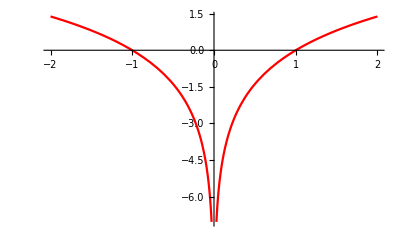
```mathematica
-Graphics-Divergent
```

```mathematica
Limit[f[x],x->0]
```

-∞

```mathematica
Clear[int1,int2]
int1[c_]:=Integrate[f[x],{x,-2,c},Assumptions->-2<c<0]
intA = Limit[int1[c],c->0,Direction->-1]
```

-4+Log[16]

```mathematica
int2[b_]:=Integrate[f[x],{x,c,2}, Assumptions->-0<c<2]
intB = Limit[int1[c],c->0,Direction->1]
```

-4+Log[16]

```mathematica
result= Simplify [intA+intB]
```

-8+Log[256]

2 (-4+c+Log[16]-c Log[c])

```mathematica
Clear[f,int,b,x]
f[x_]:=1/ (x-1)^(1/3) 
int[b_]:=Integrate[f[x],{x,4,b}, Assumptions->b>4]
Print[int[b]]
```

-3/2 (3^(2/3)-(-1+b)^(2/3))

```mathematica
Limit[int[b],b->∞]
```

∞

```mathematica
Plot[1/ (x-1)^(1/3),{x,4,1000},PlotStyle->Red,Filling->Axis,PlotRange->All]
```

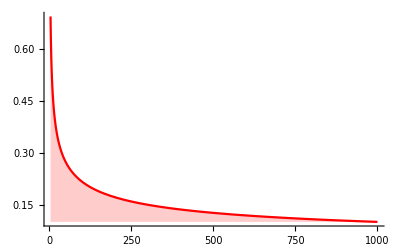
```mathematica
-Graphics-Divergent
```